```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab7\lab7

```mathematica
table = Import["errors.txt","Table"]
```

{{0.5,0.000402872},{0.25,0.0000768508},{0.125,0.0000399307},{0.0625,0.0000323705},{0.03125,0.0000305724},{0.015625,0.0000301284},{0.0078125,0.0000300178},{0.00390625,0.0000299901},{0.00195313,0.0000299832},{0.000976563,0.0000299815},{0.000488281,0.0000299811},{0.000244141,0.000029981},{0.00012207,0.0000299809},{0.0000610352,0.0000299809},{0.0000305176,0.0000299809},{0.0000152588,0.0000299809},{7.62939×10^-6,0.0000299809},{3.8147×10^-6,0.0000299809},{1.90735×10^-6,0.0000299808}}

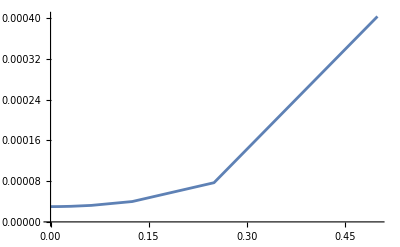

```mathematica
ListPlot[table,PlotRange->All,Joined->True]
```

```mathematica
h1 =Import["h0.1,tau0.1.txt","Table"];
h2 = Import["h0.05,tau0.025.txt","Table"];
h3=Import["h0.025,tau0.00625.txt","Table"];
h4 = Import["h0.0125,tau0.0015625.txt","Table"];
h5 = Import["h0.00625,tau0.000390625.txt","Table"];
```

```mathematica
sol = Exp[(-π^2*t)]*Sin[π*x];
```

```mathematica
gridt1 = Table[i*0.1,{i,0,1/0.1}];
gridt2 = Table[i*0.1/4,{i,0,1/(0.1/4)}];
gridt3=Table[i*0.1/16,{i,0,1/(0.1/16)}];
gridt4 = Table[i*0.1/(16*4),{i,0,1/(0.1/(16*4))}];
gridt5= Table[i*0.1/(16*16),{i,0,1/(0.1/(16*16))}];
gridx1 = Table[i*0.1,{i,0,1/0.1}];
gridx2 = Table[i*0.1/2,{i,0,1/(0.1/2)}];
gridx3 = Table[i*0.1/4,{i,0,1/(0.1/4)}];
gridx4 = Table[i*0.1/8,{i,0,1/(0.1/8)}];
gridx5 = Table[i*0.1/16,{i,0,1/(0.1/16)}];
```

```mathematica
Length@h3
```

161

```mathematica
gridt1[[5]]
```

0.4

```mathematica
gridt2[[21]]
```

0.5

```mathematica
gridt5[[1281]]
```

0.5

```mathematica
solInPoints1 = Table[sol/.t->gridt1[[5]] /. x->gridx1[[j]],{j,Length@gridx1}];
solInPoints2 = Table[sol/.t->gridt2[[21]] /. x->gridx2[[j]],{j,Length@gridx2}];
solInPoints3 = Table[sol/.t->gridt3[[81]] /. x->gridx3[[j]],{j,Length@gridx3}];
solInPoints4 = Table[sol/.t->gridt4[[321]] /. x->gridx4[[j]],{j,Length@gridx4}];
solInPoints5 = Table[sol/.t->gridt5[[1281]] /. x->gridx5[[j]],{j,Length@gridx5}];
```

```mathematica
Length@h1[[1]]
```

11

```mathematica
solInPoints2
```

{0.,0.00112506,0.00222241,0.00326505,0.00422728,0.00508543,0.00581836,0.00640801,0.00683989,0.00710334,0.00719188,0.00710334,0.00683989,0.00640801,0.00581836,0.00508543,0.00422728,0.00326505,0.00222241,0.00112506,8.80752×10^-19}

```mathematica
solInPoints1 - h1[[5]]
```

{0.,-0.0141889,-0.0269889,-0.037147,-0.043669,-0.0459163,-0.043669,-0.037147,-0.0269889,-0.0141889,2.36312×10^-18}

```mathematica
solInPoints2- h2[[21]]
```

{0.,-0.000790724,-0.00156198,-0.00229477,-0.00297106,-0.00357419,-0.00408931,-0.00450374,-0.00480727,-0.00499243,-0.00505467,-0.00499243,-0.00480727,-0.00450374,-0.00408931,-0.00357419,-0.00297106,-0.00229477,-0.00156198,-0.000790724,8.80752×10^-19}

```mathematica
Norm[solInPoints1 - h1[[5]],Infinity]
```

0.0459163

```mathematica
Norm[solInPoints2 - h2[[21]],Infinity]
```

0.00505467

```mathematica
Log[2,Norm[solInPoints1 - h1[[5]],Infinity]/Norm[solInPoints2 - h2[[21]],Infinity]]
```

3.18332

```mathematica
solInPoints3- h3[[81]]
```

{0.,-0.0000904057,-0.000180254,-0.000268991,-0.00035607,-0.000440953,-0.000523118,-0.000602057,-0.000677285,-0.000748337,-0.000814775,-0.00087619,-0.000932202,-0.000982468,-0.00102668,-0.00106455,-0.00109587,-0.00112043,-0.00113808,-0.00114871,-0.00115227,-0.00114871,-0.00113808,-0.00112043,-0.00109587,-0.00106455,-0.00102668,-0.000982468,-0.000932202,-0.00087619,-0.000814775,-0.000748337,-0.000677285,-0.000602057,-0.000523118,-0.000440953,-0.00035607,-0.000268991,-0.000180254,-0.0000904057,8.80752×10^-19}

```mathematica
Log[2,Norm[solInPoints2 - h2[[21]],Infinity]/Norm[solInPoints3- h3[[81]],Infinity]]
```

2.13314

```mathematica
Log[2,Norm[solInPoints3- h3[[81]],Infinity]/Norm[solInPoints4- h4[[321]],Infinity]]
```

2.03735

```mathematica
Log[2,Norm[solInPoints4- h4[[321]],Infinity]/Norm[solInPoints5- h5[[1281]],Infinity]]
```

2.00962

```mathematica
h1 =Import["h0.1,tau0.1.txt","Table"];
h2 = Import["h0.05,tau0.05sigma0.5.txt","Table"];
h3=Import["h0.025,tau0.025sigma0.5.txt","Table"];
h4 = Import["h0.0125,tau0.0125sigma0.5.txt","Table"];
h5 = Import["h0.00625,tau0.00625sigma0.5.txt","Table"];
```

```mathematica
gridx1 = Table[i*0.1,{i,0,1/0.1}];
gridx2 = Table[i*0.1/2,{i,0,1/(0.1/2)}];
gridx3 = Table[i*0.1/4,{i,0,1/(0.1/4)}];
gridx4 = Table[i*0.1/8,{i,0,1/(0.1/8)}];
gridx5 = Table[i*0.1/16,{i,0,1/(0.1/16)}];
gridt1 = Table[i*0.1,{i,0,1/0.1}];
gridt2 = Table[i*0.1/2,{i,0,1/(0.1/2)}];
gridt3 = Table[i*0.1/4,{i,0,1/(0.1/4)}];
gridt4 = Table[i*0.1/8,{i,0,1/(0.1/8)}];
gridt5 = Table[i*0.1/16,{i,0,1/(0.1/16)}];
```

```mathematica
solInPoints1 = Table[sol/.t->gridt1[[6]] /. x->gridx1[[j]],{j,Length@gridx1}];
solInPoints2 = Table[sol/.t->gridt2[[11]] /. x->gridx2[[j]],{j,Length@gridx2}];
solInPoints3 = Table[sol/.t->gridt3[[21]] /. x->gridx3[[j]],{j,Length@gridx3}];
solInPoints4 = Table[sol/.t->gridt4[[41]] /. x->gridx4[[j]],{j,Length@gridx4}];
solInPoints5 = Table[sol/.t->gridt5[[81]] /. x->gridx5[[j]],{j,Length@gridx5}];
```

```mathematica
gridt5[[81]]
```

0.5

```mathematica
Log[2,Norm[solInPoints1 - h1[[6]],Infinity]/Norm[solInPoints2 - h2[[11]],Infinity]]
```

5.33143

```mathematica
Log[2,Norm[solInPoints2 - h2[[11]],Infinity]/Norm[solInPoints3- h3[[21]],Infinity]]
```

1.98742

```mathematica
Log[2,Norm[solInPoints3- h3[[21]],Infinity]/Norm[solInPoints4- h4[[41]],Infinity]]
```

1.99696

```mathematica
Log[2,Norm[solInPoints4- h4[[41]],Infinity]/Norm[solInPoints5- h5[[81]],Infinity]]
```

1.99925

```mathematica
h1 =Import["h0.1,tau0.001sigma0.txt","Table"];
h2 = Import["h0.05,tau0.00025sigma0.txt","Table"];
h3=Import["h0.025,tau0.0000625sigma0.txt","Table"];
h4 = Import["h0.0125,tau0,000015625sigma0.txt","Table"];
h5 = Import["h0.00625,tau0.00000390625sigma0.txt","Table"];
```

```mathematica
gridx1 = Table[i*0.1,{i,0,1/0.1}];
gridx2 = Table[i*0.1/2,{i,0,1/(0.1/2)}];
gridx3 = Table[i*0.1/4,{i,0,1/(0.1/4)}];
gridx4 = Table[i*0.1/8,{i,0,1/(0.1/8)}];
gridx5 = Table[i*0.1/16,{i,0,1/(0.1/16)}];
gridt1 = Table[i*0.001,{i,0,1/0.001}];
gridt2 = Table[i*0.001/4,{i,0,1/(0.001/4)}];
gridt3 = Table[i*0.001/16,{i,0,1/(0.001/16)}];
gridt4 = Table[i*0.001/64,{i,0,1/(0.001/64)}];
gridt5 = Table[i*0.001/256,{i,0,1/(0.001/256)}];
```

```mathematica
gridt5[[128001]]
```

0.5

```mathematica
solInPoints1 = Table[sol/.t->gridt1[[501]] /. x->gridx1[[j]],{j,Length@gridx1}];
solInPoints2 = Table[sol/.t->gridt2[[2001]] /. x->gridx2[[j]],{j,Length@gridx2}];
solInPoints3 = Table[sol/.t->gridt3[[8001]] /. x->gridx3[[j]],{j,Length@gridx3}];
solInPoints4 = Table[sol/.t->gridt4[[32001]] /. x->gridx4[[j]],{j,Length@gridx4}];
solInPoints5 = Table[sol/.t->gridt5[[128001]] /. x->gridx5[[j]],{j,Length@gridx5}];
```

```mathematica
Log[2,Norm[solInPoints1 - h1[[501]],Infinity]/Norm[solInPoints2 - h2[[2001]],Infinity]]
```

2.01596

```mathematica
Log[2,Norm[solInPoints2 - h2[[2001]],Infinity]/Norm[solInPoints3 - h3[[8001]],Infinity]]
```

2.00398

```mathematica
Log[2,Norm[solInPoints3 - h3[[8001]],Infinity]/Norm[solInPoints4- h4[[32001]],Infinity]]
```

2.00099

```mathematica
Log[2,Norm[solInPoints4- h4[[32001]],Infinity]/Norm[solInPoints5- h5[[128001]],Infinity]]
```

2.00025